# Infinite 3D medium, Isotropic Point Source, Lambert Sphere Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine

### Namespace

```mathematica
Begin["inf3DisopointLambertSpherescatter`"]
```

inf3DisopointRayleighscatter`

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_LSscatter*"];
```

```mathematica
index[x_]:=Module[{data,α,Σt},
data=Import[x,"Table"];
Σt=data[[1,13]];
α=data[[2,3]];
{α,Σt,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
mfps=Union[#[[2]]&/@simulations]
```

{0.3,1}

```mathematica
numcollorders=simulations[[1]][[3]][[2,13]];
maxr=simulations[[1]][[3]][[2,5]];dr=simulations[[1]][[3]][[2,7]];
numr=Floor[maxr/dr];
```

## Compare MC and deterministic

### Compare moments of ϕ

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

#### mfp 1

```mathematica
mfp=1;
sims1=Select[simulations,#[[2]]==mfp&];
```

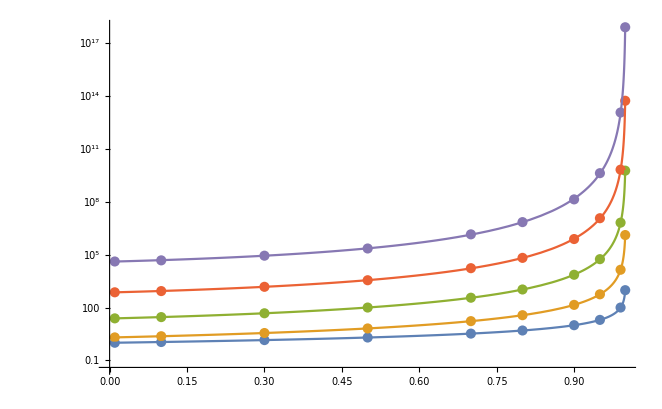

```mathematica
Show[
ListLogPlot[{
{#[[-1,2,3]],#[[-1,10,1]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,3]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,5]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,7]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,9]]}&/@sims1
}],
LogPlot[{mfp/(1-c),-3!mfp mfp^2/((-3-(4 c)/3) (-1+c)^2),5!mfp((9-(69 c)/16) mfp^4)/((-3-(4 c)/3)^2 (-5+(5 c)/16) (-1+c)^3),mfp 7!((-675+(5691 c)/8-(36399 c^2)/256-48 c^3) mfp^6)/(7 (-3-(4 c)/3)^3 (-5+(5 c)/16)^2 (-1+c)^4),mfp 9!((-496125+(52729425 c)/64-(367391171 c^2)/1024-(1099685881 c^3)/16384+(11363604819 c^4)/262144+(312487 c^5)/32-329 c^6) mfp^8)/(49 (-3-(4 c)/3)^4 (-9+c/64) (-5+(5 c)/16)^3 (-1+c)^5)},{c,0,.999},PlotRange->All]
]
```

#### mfp 0.3

```mathematica
mfp=0.3;
sims1=Select[simulations,#[[2]]==mfp&];
```

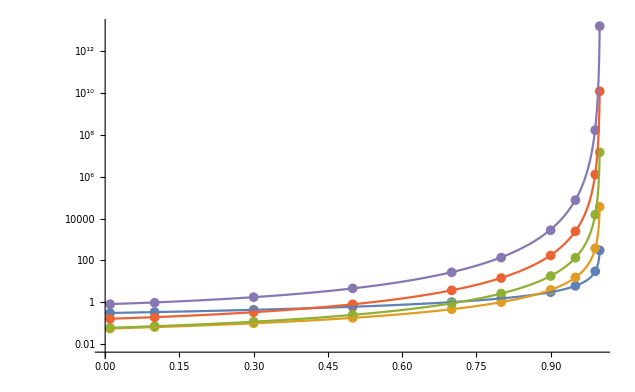

```mathematica
Show[
ListLogPlot[{
{#[[-1,2,3]],#[[-1,10,1]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,3]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,5]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,7]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,9]]}&/@sims1
}],
LogPlot[{mfp/(1-c),-3!mfp mfp^2/((-3-(4 c)/3) (-1+c)^2),5!mfp((9-(69 c)/16) mfp^4)/((-3-(4 c)/3)^2 (-5+(5 c)/16) (-1+c)^3),mfp 7!((-675+(5691 c)/8-(36399 c^2)/256-48 c^3) mfp^6)/(7 (-3-(4 c)/3)^3 (-5+(5 c)/16)^2 (-1+c)^4),mfp 9!((-496125+(52729425 c)/64-(367391171 c^2)/1024-(1099685881 c^3)/16384+(11363604819 c^4)/262144+(312487 c^5)/32-329 c^6) mfp^8)/(49 (-3-(4 c)/3)^4 (-9+c/64) (-5+(5 c)/16)^3 (-1+c)^5)},{c,0,.999},PlotRange->All]
]
```